## Umkehrfunktionen für Abbildungsformeln

### Beamer zu Kamera und umgekehrt für X-Koordinaten

```mathematica
fxk[xb_]:=1/2(b-a)xb^2+a xb
fxb[xk_]:=(-a+√(a^2+2(b-a)xk))/(b-a)
```

```mathematica
a=0.5;
b=0.3;
fxk[.5] //N
fxb[%]//N
```

0.225

0.5

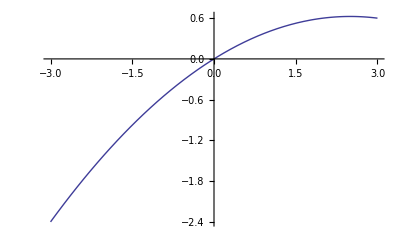

```mathematica
Plot[fxk[x],{x,-3,3}]
```

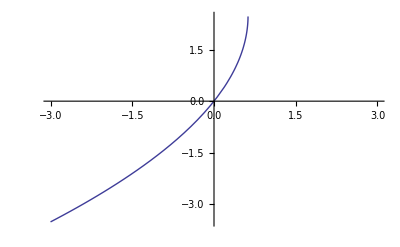

```mathematica
Plot[fxb[x],{x,-3,3}]
```

### Beamer zu Kamera und umgekehrt für Y-Koordinaten (linear)

yk0 ist der Y-Abstand zwischen den beiden parallelen Bildlinien links und rechts.
a und b sind das Abbildungsverhältnis.

```mathematica
fyk[xb_,cyb_]:=(a cyb+yk0)(1-xb)+b cyb xb
fyb[yk_,xb_]:=(yk-yk0+yk0 xb)/(a-a xb+b xb)
fyb [fyk[xb,yb],xb]//Simplify
```

yb

```mathematica
Solve[fyk[xb,y]==yk,y]/. {xb->fxb[xk]}//Simplify
```

{{y→(a yk-√(a^2-2 a xk+2 b xk) yk0+b (-yk+yk0))/((a-b) √(a^2-2 a xk+2 b xk))}}

```mathematica
a=300;
b=200;
yk0=100;
fyk[0,1]//N
fyb[%,0]//N
```

400.

1.

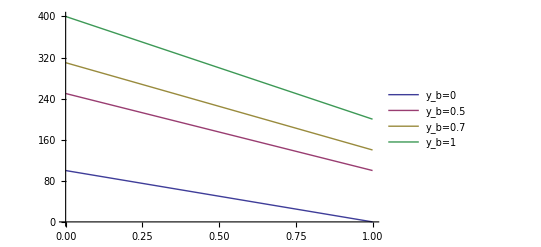

```mathematica
Plot[{fyk[xb,0],fyk[xb,0.5],fyk[xb,0.7],fyk[xb,1]},{xb,0,1},PlotLegends->{"y_b=0","y_b=0.5","y_b=0.7","y_b=1"}]
```

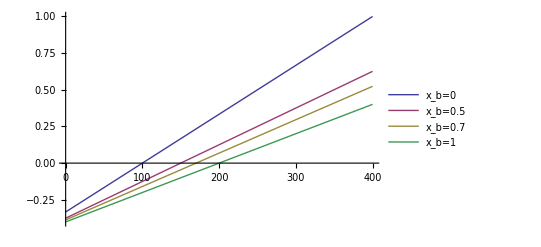

```mathematica
Plot[{fyb[yk,0],fyb[yk,0.5],fyb[yk,0.7],fyb[yk,1]},{yk,0,400},PlotLegends->{"x_b=0","x_b=0.5","x_b=0.7","x_b=1"}]
```